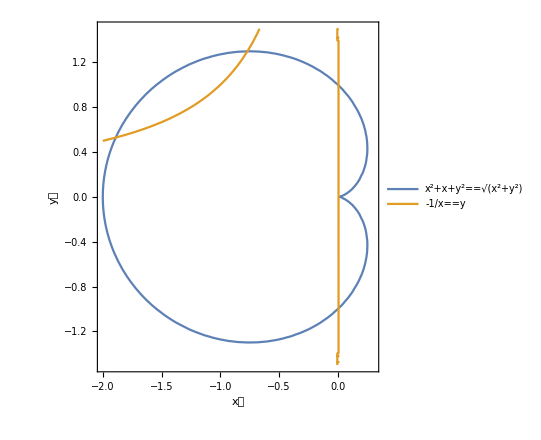

```mathematica
ContourPlot[{x^2+y^2+x==√(x^2+y^2),-1/x==y},{x,-2,0.3},{y,-1.5,1.5},Axes->True,AxesStyle->Arrowheads[{0,0.05}],AspectRatio->1.1,AxesLabel->{"x轴","y轴"},PlotTheme->"Detailed",PlotLegends->"Expressions"]
```

```mathematica
Manipulate[PolarPlot[a t,{t,-2 π,2 π},PlotTheme->"Detailed",AxesStyle->Arrowheads[{0,0.03}],PlotLabel->"阿基米德螺线",PlotLegends->None],{a,-1,1}]
```

```mathematica
Manipulate[PolarPlot[a Sin[3t],{t,0,Pi},PlotTheme->"Web",AxesStyle->Arrowheads[{0,0.03}]],{a,-1,1}]
```

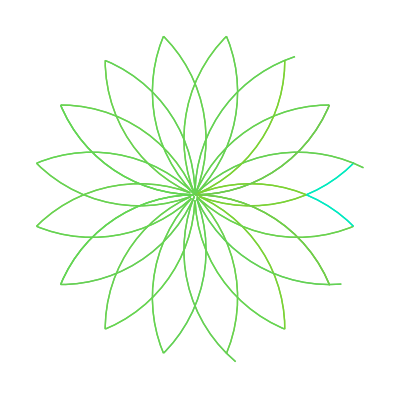

```mathematica
PolarPlot[Evaluate[Table[Abs[Sin[θ+i]],{i,0,2Pi,2Pi/16}]],{θ,0,2Pi},PlotStyle->Thick,ColorFunction->Function[{x,y,t,r},Hue[r]],Axes->False,RegionFunction->Function[{x,y,t,r},r<0.555],ColorFunctionScaling->False,PlotPoints->20,MaxRecursion->3]
```

```mathematica
PolarPlot[E^-t,{t,-Pi,Pi},PlotTheme->"Detailed",AxesStyle->Arrowheads[{0,0.03}]]
```

-Graphics-

```mathematica
PolarPlot[1/t,{t,-2Pi,2Pi},PlotTheme->"Detailed",AxesStyle->Arrowheads[{0,0.03}],AspectRatio->Full]
```

-Graphics-

隐函数作图

```mathematica
Manipulate[ContourPlot[(x^2+y^2)^2==2 a^2 x y,{x,-1,1},{y,-1,1},AspectRatio->Full,PlotTheme->"Scientific",PlotLabel->"伯努利双纽线",AxesStyle->Arrowheads[{0,0.03}]],{a,-1,1}]
```

```mathematica
Manipulate[PolarPlot[a Sin[2 t],{t,-2Pi,2Pi},PlotTheme->"Detailed",AxesStyle->Arrowheads[{0,0.03}],AspectRatio->Full,PlotStyle->{Red,Dashed},PlotLabel->"四叶玫瑰线",PlotLegends->Automatic],{a,-1,1}]
```

```mathematica
Manipulate[PolarPlot[a Sin[2 t],{t,-2Pi,2Pi},PlotTheme->"Detailed",AxesStyle->Arrowheads[{0,0.03}],AspectRatio->Full,PlotStyle->{Purple,Thickness[0.003]},PlotLabel->"四叶玫瑰线",PlotLegends->Automatic],{a,-1,1}]
```

求解方程

```mathematica
Solve[{2x+3y==8,x-2y==-3},{x,y}]
```

{{x→1,y→2}}

```mathematica
DSolve[x^3 D[y[x],{x,3}]+x^2 y''[x]-4x y'[x]==3 x^2,y[x],x]
```

{{y[x]→1/2 (-x^2+(-C[1]+ⅈ C[2])/x+1/3 x^3 (C[1]+ⅈ C[2]))+C[3]}}

```mathematica
Expand[1/2 (-x^2+(-C[1]+ⅈ C[2])/x+1/3 x^3 (C[1]+ⅈ C[2]))+C[3]]
```

-x^2/2-C[1]/(2 x)+1/6 x^3 C[1]+(ⅈ C[2])/(2 x)+1/6 ⅈ x^3 C[2]+C[3]

```mathematica
Collect[%,x]
```

```mathematica
-x^2/2+x^3 (C[1]/6+1/6 ⅈ C[2])+(-C[1]/2+1/2 ⅈ C[2])/x+C[3](*C 都表示的是常数*)
```

```mathematica
DSolve[y'[x]==3y[x]-2z[x]&&z'[x]==2y[x]-z[x]&&y[0]==1&&z[0]==0,{y,z},x]
```

{{y→Function[{x},ⅇ^x (1+2 x)],z→Function[{x},2 ⅇ^x x]}}

求积分

```mathematica
Integrate[(1+Sin[x])/(Sin[x](1+Cos[x])),x]
```

1/(2+2 Cos[x])(1-Log[Cos[x/2]]-Cos[x] Log[Cos[x/2]]+Log[Sin[x/2]]+Cos[x] Log[Sin[x/2]]+2 Sin[x])

```mathematica
Integrate[x ArcTan[x],x]
```

-x/2+ArcTan[x]/2+1/2 x^2 ArcTan[x]

```mathematica
Collect[%,ArcTan[x]]
```

-x/2+(1/2+x^2/2) ArcTan[x]

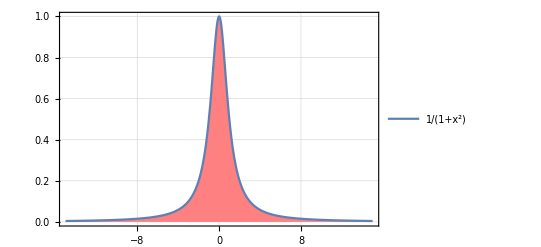

```mathematica
Plot[1/(1+x^2),{x,-15,15},PlotTheme->"Detailed",PlotRange->All,PlotRangePadding->Scaled[.05],Filling->Axis,FillingStyle->{Opacity[0.7],Pink}]
```

```mathematica
Integrate[1/(1+x^2),{x,-Infinity,Infinity}]
```

π